## Perform AUC calculations for a normal distribution

```mathematica
fx[x_]:=1/(√(2π))Exp[-1/2(x)^2];
fnormal[x_,mu_,sigma_]:=1/sigma*fx[(x-mu)/sigma];
```

### Create the normal distribution based on the normal function “fnormal”

```mathematica
normalTuple[x_,mu_,sigma_]:={x,fnormal[x,mu,sigma]};
distribution[mu_,sigma_,delta_]:=Table[normalTuple[arg,mu,sigma],{arg,-delta,delta,0.1}];
```

### Create a graphical representation of the normal distribution Set a group of testing parameters: mean μ, standard deviation σ, the “spread” of the distribution δ

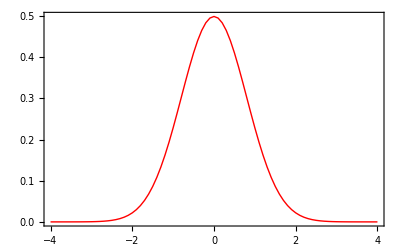

```mathematica
testParams={0,0.8,4};
distPlotter[params_]:=ListPlot[distribution[params[[1]],params[[2]],params[[3]]],Joined->True,PlotRange->All,Frame->True,Axes->False,PlotStyle->{Red,Thick}];
Show[distPlotter[testParams]]
```